```mathematica
(*{matA-> a,matC-> c,σp2-> p,σo2-> o,σff2-> m,σfb2-> n,winf-> u,wff-> v,wfb-> r,matD -> √ds,matE-> √es}*)
```

```mathematica
costTotalIndses=1/2 (1/(a^2 c^2 es)(-m+a^2 m+(-1+a^2) ds n-es o+a^2 es o-c^2 es p+√(-4 a^2 (m+ds n+es o)^2+((1+a^2) m+(1+a^2) ds n+es (o+a^2 o+c^2 p))^2)) u+1/((-1+a^2) (r+ds v))(2 (-1+a^2) n r^2+2 ((-1+a^2) m+2 (-1+a^2) ds n+(-1+a^2) es o-c^2 es p) r v+(-1+a^2) ds (m+(1+a^2) ds n+es o+a^2 (m+es o)+c^2 es p+√(-4 a^2 (m+ds n+es o)^2+((1+a^2) m+(1+a^2) ds n+es (o+a^2 o+c^2 p))^2)) v^2));
costEnergyIndses=1/(2 (-1+a^2) (r+ds v))(2 (-1+a^2) n r^2+2 ((-1+a^2) m+2 (-1+a^2) ds n+(-1+a^2) es o-c^2 es p) r v+(-1+a^2) ds (m+(1+a^2) ds n+es o+a^2 (m+es o)+c^2 es p+√(((-1+a)^2 m+(-1+a)^2 ds n+es ((-1+a)^2 o+c^2 p)) ((1+a)^2 m+(1+a)^2 ds n+es ((1+a)^2 o+c^2 p)))) v^2);
costInferenceIndses=1/(2 a^2 c^2 es)(-m+a^2 m+(-1+a^2) ds n-es o+a^2 es o-c^2 es p+√(-4 a^2 (m+ds n+es o)^2+((1+a^2) m+(1+a^2) ds n+es (o+a^2 o+c^2 p))^2)) u;
costFBEnergyIndses=n r+1/(8 a^2 (1-a^2) (m+ds n+es o)^2 (r+ds v)^2)ds (-m+a^2 m+(-1+a^2) ds n-es o+a^2 es o-c^2 es p+√(-4 a^2 (m+ds n+es o)^2+((1+a^2) m+(1+a^2) ds n+es (o+a^2 o+c^2 p))^2))^2 (m+a^2 m+ds n+a^2 ds n+es o+a^2 es o+c^2 es p+√(-4 a^2 (m+ds n+es o)^2+((1+a^2) m+(1+a^2) ds n+es (o+a^2 o+c^2 p))^2)) r v^2;
matK11Indses=(-m+a^2 m+(-1+a^2) ds n-es o+a^2 es o-c^2 es p+√(-4 a^2 (m+ds n+es o)^2+((1+a^2) m+(1+a^2) ds n+es (o+a^2 o+c^2 p))^2))/(2 a^2 c √es (m+ds n+es o));
matHaug11Indses=-((√ds (-m+a^2 m+(-1+a^2) ds n-es o+a^2 es o-c^2 es p+√(-4 a^2 (m+ds n+es o)^2+((1+a^2) m+(1+a^2) ds n+es (o+a^2 o+c^2 p))^2)))/(2 a^2 c √es (m+ds n+es o)));
matFaug11Indses=1/(2 a (m+ds n+es o))(m+a^2 m+(1+a^2) ds n+es o+a^2 es o+c^2 es p-√(-4 a^2 (m+ds n+es o)^2+((1+a^2) m+(1+a^2) ds n+es (o+a^2 o+c^2 p))^2));
matL11Indses=-(a c √ds √es v)/(r+ds v);
repeat[m_,n_Integer?Positive]:=Sequence@@ConstantArray[m,n]
matFaug11InSqDE = matFaug11;
matHaug11InSqDE = matHaug11;
matK11InSqDE = matK11;
matL11InSqDE = matL11;
```

### Plots w.r.t change in wfb

```mathematica
(*{matA-> a,matC-> c,σp2-> p,σo2-> o,σff2-> m,σfb2-> n,winf-> u,wff-> v,wfb-> r}*)
```

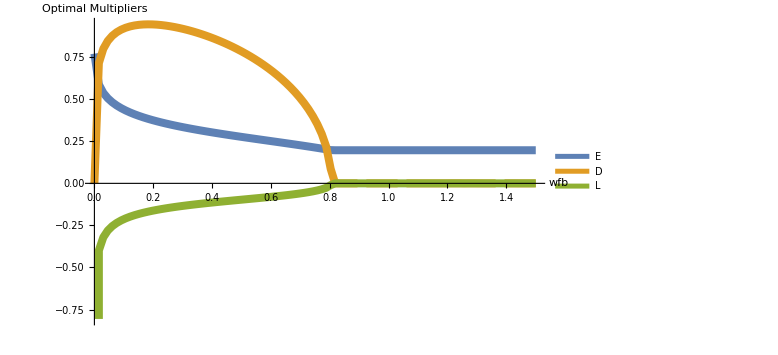

```mathematica
minVal =0;
maxVal=1.5;
noPoints = 100;
{iList,params,dsList,esList,dList,eList,matFstarList,matHstarList,matGstarList,matLstarList,costTotalIndsesList,costFBEnergyIndsesList,costEnergyIndsesList,costInferenceIndsesList}={repeat[zeroList,14]}/.{zeroList-> Table[0,noPoints]};
For[i=1,i<(noPoints+1),i++,
iList[[i]]=(maxVal-minVal)/(noPoints-1)(i-1)+minVal;evAt={a->.999,c-> .5,p->.1,o-> .1,m-> .1,r->iList[[i]],u-> 1,v->1,n-> .1};params[[i]]=Minimize[costTotalIndses/.evAt,{ds≥0,es≥0},{ds,es}][[2]];
{dsList[[i]],esList[[i]]}={ds,es}/.params[[i]];
dList[[i]]= Sqrt[dsList[[i]]];
eList[[i]]= Sqrt[esList[[i]]];
{costEnergyIndsesList[[i]],costInferenceIndsesList[[i]],costFBEnergyIndsesList[[i]],matFstarList[[i]],matHstarList[[i]],matGstarList[[i]],matLstarList[[i]]}={costEnergyIndses,costInferenceIndses,costFBEnergyIndses,matFaug11Indses,matHaug11Indses,matK11Indses,matL11Indses}/.evAt/.{ds->dsList[[i]],es->  esList[[i]]};
costTotalIndsesList[[i]]=costEnergyIndsesList[[i]]+ costInferenceIndsesList[[i]];]
wfbList=iList;
wfbmatLstarList=Re[matLstarList];
wfbmatDList=Re[dList];
wfbmatEList=Re[eList];
ListLinePlot[{Transpose@{iList,eList},Transpose@{iList,dList},Transpose@{iList,Re[matLstarList]}},PlotStyle->Thickness[.01],ImageSize-> Large,Ticks->None,PlotLegends->{"E", "D","L"},AxesLabel->{"wfb", "Optimal Multipliers"}]
```

### Plots w.r.t change in σfb2

```mathematica
(*{matA-> a,matC-> c,σp2-> p,σo2-> o,σff2-> m,σfb2-> n,winf-> u,wff-> v,wfb-> r}*)
```

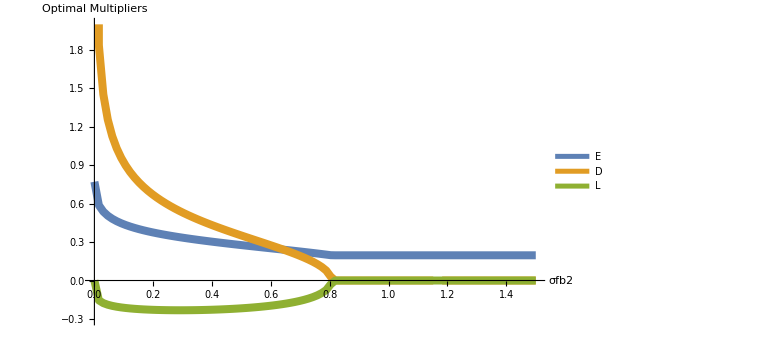

```mathematica
minVal =0;
maxVal=1.5;
noPoints = 100;
{iList,params,dsList,esList,dList,eList,matFstarList,matHstarList,matGstarList,matLstarList,costTotalIndsesList,costFBEnergyIndsesList,costEnergyIndsesList,costInferenceIndsesList}={repeat[zeroList,14]}/.{zeroList-> Table[0,noPoints]};
For[i=1,i<(noPoints+1),i++,
iList[[i]]=(maxVal-minVal)/(noPoints-1)(i-1)+minVal;evAt={a->.999,c-> .5,p->.1,o-> .1,m-> .1,r->.1,u-> 1,v->1,n-> iList[[i]]};params[[i]]=Minimize[costTotalIndses/.evAt,{ds≥0,es≥0},{ds,es}][[2]];
{dsList[[i]],esList[[i]]}={ds,es}/.params[[i]];
dList[[i]]= Sqrt[dsList[[i]]];
eList[[i]]= Sqrt[esList[[i]]];
{costEnergyIndsesList[[i]],costInferenceIndsesList[[i]],costFBEnergyIndsesList[[i]],matFstarList[[i]],matHstarList[[i]],matGstarList[[i]],matLstarList[[i]]}={costEnergyIndses,costInferenceIndses,costFBEnergyIndses,matFaug11Indses,matHaug11Indses,matK11Indses,matL11Indses}/.evAt/.{ds->dsList[[i]],es->  esList[[i]]};
costTotalIndsesList[[i]]=costEnergyIndsesList[[i]]+ costInferenceIndsesList[[i]];]
σfb2List=iList;
σfb2matLstarList=Re[matLstarList];
σfb2matDList=Re[dList];
σfb2matEList=Re[eList];
ListLinePlot[{Transpose@{iList,eList},Transpose@{iList,dList},Transpose@{iList,Re[matLstarList]}},PlotStyle->Thickness[.01],ImageSize-> Large,Ticks->None,PlotRange->{-.3,2},PlotLegends->{"E", "D","L"},AxesLabel->{"σfb2", "Optimal Multipliers"}]
```

### Plots w.r.t change in wff

```mathematica
(*{matA-> a,matC-> c,σp2-> p,σo2-> o,σff2-> m,σfb2-> n,winf-> u,wff-> v,wfb-> r}*)
```

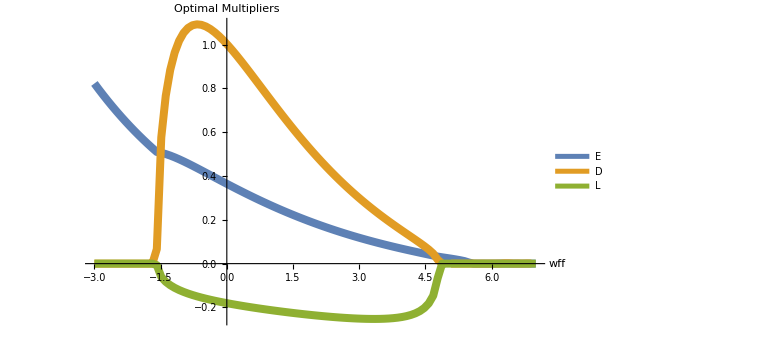

```mathematica
minVal =-3;
maxVal=7;
noPoints = 100;
{iList,params,dsList,esList,dList,eList,matFstarList,matHstarList,matGstarList,matLstarList,costTotalIndsesList,costFBEnergyIndsesList,costEnergyIndsesList,costInferenceIndsesList}={repeat[zeroList,14]}/.{zeroList-> Table[0,noPoints]};
For[i=1,i<(noPoints+1),i++,
iList[[i]]=(maxVal-minVal)/(noPoints-1)(i-1)+minVal;evAt={a->.99,c-> 1,p->.1,o-> .1,m-> 1,r->1,u-> 1,v->Exp[iList[[i]]],n-> .1};params[[i]]=Minimize[costTotalIndses/.evAt,{ds≥0,es≥0},{ds,es}][[2]];
{dsList[[i]],esList[[i]]}={ds,es}/.params[[i]];
dList[[i]]= Sqrt[dsList[[i]]];
eList[[i]]= Sqrt[esList[[i]]];
{costEnergyIndsesList[[i]],costInferenceIndsesList[[i]],costFBEnergyIndsesList[[i]],matFstarList[[i]],matHstarList[[i]],matGstarList[[i]],matLstarList[[i]]}={costEnergyIndses,costInferenceIndses,costFBEnergyIndses,matFaug11Indses,matHaug11Indses,matK11Indses,matL11Indses}/.evAt/.{ds->dsList[[i]],es->  esList[[i]]};
costTotalIndsesList[[i]]=costEnergyIndsesList[[i]]+ costInferenceIndsesList[[i]];]
wffLogList=iList;
wffmatLstarList=Re[matLstarList];
wffmatDList=Re[dList];
wffmatEList=Re[eList];
ListLinePlot[{Transpose@{iList,eList},Transpose@{iList,dList},Transpose@{iList,Re[matLstarList]}},PlotStyle->Thickness[.01],ImageSize-> Large,Ticks->None,PlotLegends->{"E", "D","L"},AxesLabel->{"wff", "Optimal Multipliers"}]
```

### Plots w.r.t change in σff2

```mathematica
(*{matA-> a,matC-> c,σp2-> p,σo2-> o,σff2-> m,σfb2-> n,winf-> u,wff-> v,wfb-> r}*)
```

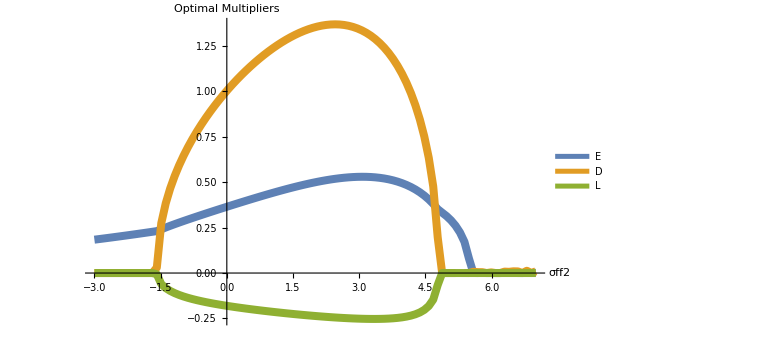

```mathematica
minVal =-3;
maxVal=7;
noPoints = 100;
{iList,params,dsList,esList,dList,eList,matFstarList,matHstarList,matGstarList,matLstarList,costTotalIndsesList,costFBEnergyIndsesList,costEnergyIndsesList,costInferenceIndsesList}={repeat[zeroList,14]}/.{zeroList-> Table[0,noPoints]};
For[i=1,i<(noPoints+1),i++,
iList[[i]]=(maxVal-minVal)/(noPoints-1)(i-1)+minVal;evAt={a->.99,c-> 1,p->.1,o-> .1,m-> Exp[iList[[i]]],r->1,u-> 1,v->1,n-> .1};params[[i]]=Minimize[costTotalIndses/.evAt,{ds≥0,es≥0},{ds,es}][[2]];
{dsList[[i]],esList[[i]]}={ds,es}/.params[[i]];
dList[[i]]= Sqrt[dsList[[i]]];
eList[[i]]= Sqrt[esList[[i]]];
{costEnergyIndsesList[[i]],costInferenceIndsesList[[i]],costFBEnergyIndsesList[[i]],matFstarList[[i]],matHstarList[[i]],matGstarList[[i]],matLstarList[[i]]}={costEnergyIndses,costInferenceIndses,costFBEnergyIndses,matFaug11Indses,matHaug11Indses,matK11Indses,matL11Indses}/.evAt/.{ds->dsList[[i]],es->  esList[[i]]};
costTotalIndsesList[[i]]=costEnergyIndsesList[[i]]+ costInferenceIndsesList[[i]];]
σff2LogList=iList;
σff2matLstarList=Re[matLstarList];
σff2matDList=Re[dList];
σff2matEList=Re[eList];
ListLinePlot[{Transpose@{iList,eList},Transpose@{iList,dList},Transpose@{iList,Re[matLstarList]}},PlotStyle->Thickness[.01],ImageSize-> Large,Ticks->None,PlotLegends->{"E", "D","L"},AxesLabel->{"σff2", "Optimal Multipliers"}]
```